```mathematica
$Assumptions=And[s>0,α>1,M>2,M∈Integers,q>0,q<1];
```

```mathematica
ys=y/.FindRoot[y==Tanh[y/2]Cosh[y],{y,2}]
```

1.50553

```mathematica
1/(2*ys^2)
```

0.220591

```mathematica
ABηsol=Solve[{(α^2-α+1)η-α^2 A-B==0,
-q α η+(1+(q-1)α)A+(α+q-1)B==0,
α^(M/2)A+α^(1-M/2)B==-(2α)/((α+1)s)},{A,B,η}][[1]]
```

{A→-(2 α^(1+M/2) (1-q-α+q α+α^2))/(s (1+α) (α-α^2+q α^2+α^3+α^M-q α^M-α^(1+M)+q α^(1+M)+α^(2+M))),B→-(2 α^(1+M/2) (1-α+q α+α^2))/(s (1+α) (α-α^2+q α^2+α^3+α^M-q α^M-α^(1+M)+q α^(1+M)+α^(2+M))),η→-(2 α^(1+M/2) (1+q α+α^2))/(s (1+α) (α-α^2+q α^2+α^3+α^M-q α^M-α^(1+M)+q α^(1+M)+α^(2+M)))}

```mathematica
FullSimplify[η/.ABηsol]
```

-(2 α^(1+M/2) (1+α (q+α)))/(s (α+q α^2+q α^3+α^4-(-1+q) α^M+q α^(2+M)+α^(3+M)))

```mathematica
lapl=FullSimplify[2/(M-2(1-q))(1/s+q η+(1-q)(α A+B/α))/.ABηsol]
```

(2 (α+q α^2+q α^3+α^4+2 α^(M/2) (-1+q (-1+α)^2+α-α^2) (1+α (q+α))+α^M (1+α^3+q (-1+α^2))))/((-2+M+2 q) s (1+α) (α+(-1+q) α^2+α^3+α^M (1+q (-1+α)+(-1+α) α)))

```mathematica
qder=D[lapl,q]//FullSimplify
```

(2 (-(-2+M+2 q) (α^2+(-1+α) α^M) (α+q α^2+q α^3+α^4+2 α^(M/2) (-1+q (-1+α)^2+α-α^2) (1+α (q+α))+α^M (1+α^3+q (-1+α^2)))-2 (α+(-1+q) α^2+α^3+α^M (1+q (-1+α)+(-1+α) α)) (α+q α^2+q α^3+α^4+2 α^(M/2) (-1+q (-1+α)^2+α-α^2) (1+α (q+α))+α^M (1+α^3+q (-1+α^2)))+(-2+M+2 q) (α+(-1+q) α^2+α^3+α^M (1+q (-1+α)+(-1+α) α)) (α^2 (1+α)+α^M (-1+α^2)+2 α^(M/2) (1+α (-3+2 q (-1+α)^2+α (3+(-3+α) α))))))/((-2+M+2 q)^2 s (1+α) (α+(-1+q) α^2+α^3+α^M (1+q (-1+α)+(-1+α) α))^2)

```mathematica
qsol=Solve[qder==0,q]
```

{{q→(2 α^3+2 α^6-2 M α^(2+M/2)-8 α^(3+M/2)+6 M α^(3+M/2)+8 α^(4+M/2)-8 M α^(4+M/2)-8 α^(5+M/2)+6 M α^(5+M/2)-2 M α^(6+M/2)+4 α^(3 M/2)-2 α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(4+M)+4 α^(5+M)-4 α^(1+(3 M)/2)-2 M α^(1+(3 M)/2)+6 M α^(2+(3 M)/2)+4 α^(3+(3 M)/2)-8 M α^(3+(3 M)/2)-4 α^(4+(3 M)/2)+6 M α^(4+(3 M)/2)-2 M α^(5+(3 M)/2)+2 α^(1+2 M)-2 α^(3+2 M)+2 α^(4+2 M)-√((-2 α^3-2 α^6+2 M α^(2+M/2)+8 α^(3+M/2)-6 M α^(3+M/2)-8 α^(4+M/2)+8 M α^(4+M/2)+8 α^(5+M/2)-6 M α^(5+M/2)+2 M α^(6+M/2)-4 α^(3 M/2)+2 α^(2 M)+2 α^(1+M)-4 α^(2+M)+2 α^(4+M)-4 α^(5+M)+4 α^(1+(3 M)/2)+2 M α^(1+(3 M)/2)-6 M α^(2+(3 M)/2)-4 α^(3+(3 M)/2)+8 M α^(3+(3 M)/2)+4 α^(4+(3 M)/2)-6 M α^(4+(3 M)/2)+2 M α^(5+(3 M)/2)-2 α^(1+2 M)+2 α^(3+2 M)-2 α^(4+2 M))^2-4 (-α^4-α^5-2 α^(3+M/2)+M α^(3+M/2)+6 α^(4+M/2)-2 M α^(4+M/2)-2 α^(5+M/2)+M α^(5+M/2)+2 α^(3 M/2)-α^(2 M)+2 α^(2+M)-2 α^(4+M)-4 α^(1+(3 M)/2)-M α^(1+(3 M)/2)+3 M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)-3 M α^(3+(3 M)/2)+M α^(4+(3 M)/2)+α^(1+2 M)+α^(2+2 M)-α^(3+2 M)) (-α^2+α^3-α^4-α^5+α^6-α^7+M α^(1+M/2)+2 α^(2+M/2)-3 M α^(2+M/2)-4 α^(3+M/2)+6 M α^(3+M/2)+6 α^(4+M/2)-7 M α^(4+M/2)-4 α^(5+M/2)+6 M α^(5+M/2)+2 α^(6+M/2)-3 M α^(6+M/2)+M α^(7+M/2)+2 α^(3 M/2)-α^(2 M)-2 α^(1+M)+2 α^(2+M)-2 α^(3+M)-2 α^(4+M)+2 α^(5+M)-2 α^(6+M)-2 M α^(1+(3 M)/2)+4 M α^(2+(3 M)/2)+4 α^(3+(3 M)/2)-6 M α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+5 M α^(4+(3 M)/2)+2 α^(5+(3 M)/2)-3 M α^(5+(3 M)/2)+M α^(6+(3 M)/2)+α^(1+2 M)-α^(2+2 M)-α^(3+2 M)+α^(4+2 M)-α^(5+2 M))))/(2 (-α^4-α^5-2 α^(3+M/2)+M α^(3+M/2)+6 α^(4+M/2)-2 M α^(4+M/2)-2 α^(5+M/2)+M α^(5+M/2)+2 α^(3 M/2)-α^(2 M)+2 α^(2+M)-2 α^(4+M)-4 α^(1+(3 M)/2)-M α^(1+(3 M)/2)+3 M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)-3 M α^(3+(3 M)/2)+M α^(4+(3 M)/2)+α^(1+2 M)+α^(2+2 M)-α^(3+2 M)))},{q→(2 α^3+2 α^6-2 M α^(2+M/2)-8 α^(3+M/2)+6 M α^(3+M/2)+8 α^(4+M/2)-8 M α^(4+M/2)-8 α^(5+M/2)+6 M α^(5+M/2)-2 M α^(6+M/2)+4 α^(3 M/2)-2 α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(4+M)+4 α^(5+M)-4 α^(1+(3 M)/2)-2 M α^(1+(3 M)/2)+6 M α^(2+(3 M)/2)+4 α^(3+(3 M)/2)-8 M α^(3+(3 M)/2)-4 α^(4+(3 M)/2)+6 M α^(4+(3 M)/2)-2 M α^(5+(3 M)/2)+2 α^(1+2 M)-2 α^(3+2 M)+2 α^(4+2 M)+√((-2 α^3-2 α^6+2 M α^(2+M/2)+8 α^(3+M/2)-6 M α^(3+M/2)-8 α^(4+M/2)+8 M α^(4+M/2)+8 α^(5+M/2)-6 M α^(5+M/2)+2 M α^(6+M/2)-4 α^(3 M/2)+2 α^(2 M)+2 α^(1+M)-4 α^(2+M)+2 α^(4+M)-4 α^(5+M)+4 α^(1+(3 M)/2)+2 M α^(1+(3 M)/2)-6 M α^(2+(3 M)/2)-4 α^(3+(3 M)/2)+8 M α^(3+(3 M)/2)+4 α^(4+(3 M)/2)-6 M α^(4+(3 M)/2)+2 M α^(5+(3 M)/2)-2 α^(1+2 M)+2 α^(3+2 M)-2 α^(4+2 M))^2-4 (-α^4-α^5-2 α^(3+M/2)+M α^(3+M/2)+6 α^(4+M/2)-2 M α^(4+M/2)-2 α^(5+M/2)+M α^(5+M/2)+2 α^(3 M/2)-α^(2 M)+2 α^(2+M)-2 α^(4+M)-4 α^(1+(3 M)/2)-M α^(1+(3 M)/2)+3 M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)-3 M α^(3+(3 M)/2)+M α^(4+(3 M)/2)+α^(1+2 M)+α^(2+2 M)-α^(3+2 M)) (-α^2+α^3-α^4-α^5+α^6-α^7+M α^(1+M/2)+2 α^(2+M/2)-3 M α^(2+M/2)-4 α^(3+M/2)+6 M α^(3+M/2)+6 α^(4+M/2)-7 M α^(4+M/2)-4 α^(5+M/2)+6 M α^(5+M/2)+2 α^(6+M/2)-3 M α^(6+M/2)+M α^(7+M/2)+2 α^(3 M/2)-α^(2 M)-2 α^(1+M)+2 α^(2+M)-2 α^(3+M)-2 α^(4+M)+2 α^(5+M)-2 α^(6+M)-2 M α^(1+(3 M)/2)+4 M α^(2+(3 M)/2)+4 α^(3+(3 M)/2)-6 M α^(3+(3 M)/2)-2 α^(4+(3 M)/2)+5 M α^(4+(3 M)/2)+2 α^(5+(3 M)/2)-3 M α^(5+(3 M)/2)+M α^(6+(3 M)/2)+α^(1+2 M)-α^(2+2 M)-α^(3+2 M)+α^(4+2 M)-α^(5+2 M))))/(2 (-α^4-α^5-2 α^(3+M/2)+M α^(3+M/2)+6 α^(4+M/2)-2 M α^(4+M/2)-2 α^(5+M/2)+M α^(5+M/2)+2 α^(3 M/2)-α^(2 M)+2 α^(2+M)-2 α^(4+M)-4 α^(1+(3 M)/2)-M α^(1+(3 M)/2)+3 M α^(2+(3 M)/2)+2 α^(3+(3 M)/2)-3 M α^(3+(3 M)/2)+M α^(4+(3 M)/2)+α^(1+2 M)+α^(2+2 M)-α^(3+2 M)))}}

```mathematica
q1=FullSimplify[q/.qsol[[1]]]
```

(α^(2+M/2) (M (-1+α)^2+4 α) (1+(-1+α) α)+(-1+α) α^(3 M/2) (2+(2+M (-1+α)) α) (1+(-1+α) α)-α^3 (1+α^3)+α^(1+M) (1-2 α+α^3-2 α^4)-α^(2 M) (-1+α-α^3+α^4)+√(α^(1+M/2) (1+(-1+α) α) (-α^3+α^M) (1+(-1+α) (α+α^M)) (α (1+α) (2-M α+2 α^2)+α^M (1+α) (M-M α+2 α^2)+α^(M/2) (M (-1+α)^2+2 α) (-2+α (M-2 (1+α))))))/(α^4 (1+α)+(-1+α)^2 α^(2 M) (1+α)+2 α^(2+M) (-1+α^2)+α^(3+M/2) (-M (-1+α)^2+2 (1+(-3+α) α))-(-1+α) α^(3 M/2) (-2+α (M (-1+α)^2+2 (1+α))))

```mathematica
q2=FullSimplify[q/.qsol[[2]]]
```

(α^(2+M/2) (M (-1+α)^2+4 α) (1+(-1+α) α)+(-1+α) α^(3 M/2) (2+(2+M (-1+α)) α) (1+(-1+α) α)-α^3 (1+α^3)+α^(1+M) (1-2 α+α^3-2 α^4)-α^(2 M) (-1+α-α^3+α^4)-√(α^(1+M/2) (1+(-1+α) α) (-α^3+α^M) (1+(-1+α) (α+α^M)) (α (1+α) (2-M α+2 α^2)+α^M (1+α) (M-M α+2 α^2)+α^(M/2) (M (-1+α)^2+2 α) (-2+α (M-2 (1+α))))))/(α^4 (1+α)+(-1+α)^2 α^(2 M) (1+α)+2 α^(2+M) (-1+α^2)+α^(3+M/2) (-M (-1+α)^2+2 (1+(-3+α) α))-(-1+α) α^(3 M/2) (-2+α (M (-1+α)^2+2 (1+α))))

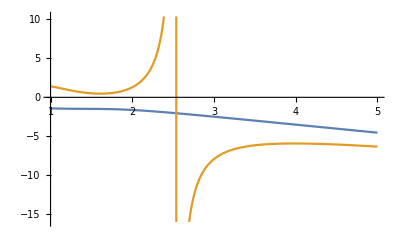

```mathematica
Plot[{q1/.M->4,q2/.M->4},{α,1,5}]
```

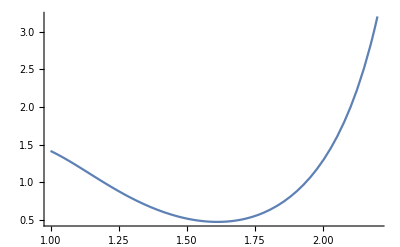

```mathematica
Plot[q2/.M->4,{α,1,2.2}]
```